# FREQUENCY MODULATION DYNAMIC FORCE SPECTROSCOPY Sader-Jarvis Method with Inflection Point Test for Automated Valid Force Measurements Force vs distance from frequency shift vs distance data Mathematica 12.1 Version 1.2 - John Sader (15 September 2020) REFERENCES: JE Sader et al., Applied Physics Letters, 84, 1801-1803 (2004); Nature Nanotechnology, 13, 1088-1091 (2018); Review of Scientific Instruments, this submission.

Mathematica notebook implementation of the Sader-Jarvis method [Sader et al., Applied Physics Letters, 84, 1801 (2004)] with inflection point test [Sader et al., Nature Nanotechnology, 13, 1088 (2018)].

1. Sader-Jarvis method determines force vs distance from measured frequency shift vs distance data, obtained using frequency modulation atomic force microscopy measurements; procedure is for any amplitude of oscillation.
2. Inflection point test assesses validity of recovered force vs distance, and guides users outside of the forbidden amplitude zone.

INSTRUCTIONS
(1) Enter measurement operating conditions and frequency vs distance data under “INPUT”.
[The frequency shift vs distance data file must contain two columns: left is distance (metres), right is frequency shift (Hz). Distance should increase with increasing line number in the data file. Smaller distances corresponds to tip being closer to the sample.]
(2) Select all headings — Command-A (Mac) or CRTL-A (PC) — and execute using Enter.

OUTPUT:  Recovered force curve (saved as SJ_Force.csv in current directory), its validity and appropriate amplitudes for valid force measurements.

NOTE:  Smallest distance in force curve is set to zero by the code.

## INPUT

#### DEFINITIONS - nanometre (nm), Angstrom (Å), picometre (pm)

```mathematica
nm=10^-9.;Å=10^-10.;pm=10^-12.;
```

#### Oscillation amplitude (m)

```mathematica
amp=1Å;
```

#### Cantilever spring constant (N/m)

```mathematica
kspring = 2000;
```

#### Resonant frequency far from surface (Hz)

```mathematica
f0=20000;
```

#### Frequency shift (Hz) vs distance (m) data file

```mathematica
SetSystemOptions["CompileOptions" ->"TableCompileLength"->Infinity];SetSystemOptions["CompileOptions" ->"ArrayCompileLength"->Infinity];
```

Data file

```mathematica
SetDirectory[NotebookDirectory[]];
data =dataload= ReadList["Z-Spectroscopy_BP_00188_z.txt", Number, RecordLists->True];
```

#### Other operating parameters (advanced users only)

Sader-Jarvis method

Smoothing  - number of nearest neighbour points to average frequency shift vs distance curve:

```mathematica
set = 0;
```

Frequency offset at large distances. Ensures frequency shift in data is zero at large separations. (Hz):

```mathematica
freqoffset = 0;
```

Force conversion - (Yes = 1; No = 0):

```mathematica
Forceconvert = 1;
```

Energy conversion - (Yes = 1; No = 0):

```mathematica
Energyconvert = 0;
```

Inflection point test

Minimum required force jump through inflection point for significant ill-posed effect. Fraction of maximum force (not less than 0.1)

```mathematica
forcejumpminimum=0.1;
```

Force noise threshold - below which an inflection point search is not performed (nominally set at 5%)

```mathematica
forcethreshold=0.05;
```

Minimum number of data points either size of inflection point to perform polynomial fit (minimum = 5 needed)

```mathematica
mindefault=5;
```

Maximum number of data points either size of inflection point to perform polynomial fit

```mathematica
maxdefault=10;
```

Use automatic estimate of maximum number of data points to perform polynomial fit (True = 1. False = 0)

```mathematica
automax=1;
```

Show intermediate fitting results of inflection point test at each infection point (True = 1. False = 0)

```mathematica
showintermediatesteps=1;
```

## Sader-Jarvis method

### Data checking, smoothing algorithm and numerical derivative calculation

#### Data checking

Following procedure checks that separation is increasing with line number - if this is not the case it sorts the datafile in order of increasing separation.
Also checks that each separation value is unique, and eliminates non-unique separation values:

```mathematica
len = Length[data]; 
errororder = 0; 
checkeliminate = 0;

m = 1;
    For[i = 1, i <= len - 1, i++,
	If[data[[i + 1, 1]] < data[[i, 1]], lineerror[m] = i; m += 1; errororder = 1]];
m -= 1;

If[errororder == 1, 
(*
Print["WARNING: Input datafile. Separation not increasing with increasing line number! See line number(s):", Array[lineerror, m]];
Print["WARNING: Input datafile has been sorted in order of increasing separation"];
*)
 data = Sort[data];
];

n = 1; 
For[i = 1, i <= len - 1, i++,
	If[data[[i + 1, 1]] == data[[i, 1]], reset[n] = i + 1; n += 1; checkeliminate = 1]];
n -= 1;

tabdelete = Table[{reset[j]}, {j, 1, n}];
data = Delete[data, tabdelete];

(* If[checkeliminate == 1, Print["WARNING: Repeated separation values have been eliminated."]]; *)

ClearAll[m, n, i, j, len];
```

Converts datafile into Δf/f vs separation(m) data, and normalises separation so that zero separation corresponds to smallest separation:

```mathematica
datanew = Table[{data[[i, 1]] - data[[1, 1]] , data[[i, 2]] / f0 - freqoffset / f0}, {i, 1, Length[data]}];
data = datafreq=datanew;
```

Plot of frequency vs separation data is given in "Plotting results" heading.

#### Smoothing procedure (repeats procedure once):

```mathematica
data1 = Table[{data[[i, 1]], 1 / (2 set + 1) Sum[data[[i + n, 2]], {n, -set, set}]},  {i, set + 1, Length[data] - set}];
data2 =  Table[{data1[[i, 1]], 1 / (2 set + 1) Sum[data1[[i + n, 2]], {n, -set, set}]},  {i, set + 1, Length[data1] - set}];

smooth = Table[data2[[i]], {i, 2, Length[data2] - 1}];
```

#### Numerical derivative computation:

```mathematica
deriv = Table[{data2[[i, 1]], (data2[[i+1, 2]] - data2[[i - 1, 2]]) / (data2[[i+1, 1]] - data2[[i - 1, 1]])}, {i, 2, Length[data2] - 1}];
```

Plot of smoothed data and its derivative given in "Plotting results" heading.

### Force evaluation

Evaluates integral to determine force vs separation data from frequency shift vs separation data.

Coefficients (executed immediately prior to force calculation below)

```mathematica
InitializeCoeffF := Module[{tmp},
coeffF1=Sqrt[amp/π] / 8;
coeffF2=Sqrt[amp]^3 /Sqrt[2];
coeffF3=Sqrt[amp/π] / 4;
coeffF4=- Sqrt[2]Sqrt[amp]^3;
];
```

Integrand

```mathematica
inttableF[z_] := Table[{smooth[[t, 1]], (1 +  coeffF1 / Sqrt[smooth[[t, 1]] - smooth[[z, 1]]]) smooth[[t, 2]] - coeffF2 / Sqrt[smooth[[t, 1]] - smooth[[z, 1]]] deriv[[t, 2]]}, {t, z+1, Length[smooth]}];
```

These functions account for the integrable singularity at t = z:

```mathematica
correctF0[z_] := smooth[[z, 2]] (smooth[[z+1, 1]] - smooth[[z, 1]]);
correctF1[z_] := coeffF3 smooth[[z, 2]] Sqrt[smooth[[z+1, 1]] - smooth[[z, 1]]];
correctF2[z_] := coeffF4 deriv[[z, 2]] Sqrt[smooth[[z+1, 1]] - smooth[[z, 1]]];
```

Complete integral expression for force:

```mathematica
intF[z_] := Module[{datasub,dataxmin,dataxmax,ListInt}, 
datasub=inttableF[z];
dataxmin=datasub[[1, 1]];
dataxmax=datasub[[Length[datasub], 1]];
ListInt=Integrate[Interpolation[datasub, InterpolationOrder->2][x], {x, dataxmin, dataxmax}];
2 kspring (correctF0[z] + correctF1[z] + correctF2[z] + ListInt)
];
```

Evaluates force vs separation:

```mathematica
(* Turn off warning message for Interpolation for for requested order is too high *)
Off[Interpolation::inhr];
```

```mathematica
If[Forceconvert == 1, InitializeCoeffF; Forcedata = Table[{smooth[[z, 1]], intF[z]}, {z, 1, Length[smooth] - 1}]];
```

Plot of force data given in "Plotting results" heading.

### Energy evaluation

Evaluates integral to determine force vs separation data from frequency shift vs separation data.

Coefficients (executed immediately prior to energy calculation below)

```mathematica
InitializeCoeffE := Module[{tmp},
coeffE1=Sqrt[amp/π] / 4;
coeffE2=Sqrt[amp]^3/Sqrt[2];
coeffE3=1/2 ;
coeffE4=Sqrt[amp/π] / 6 ;
coeffE5=Sqrt[2] Sqrt[amp]^3;
];
```

Integrand

```mathematica
inttableE[z_] := Module[{ssz1},
ssz1=smooth[[z, 1]];
Table[{smooth[[t, 1]], smooth[[t, 2]] ((smooth[[t, 1]] - ssz1) + coeffE1  Sqrt[smooth[[t, 1]] - ssz1] + coeffE2 / Sqrt[smooth[[t, 1]] - ssz1])}, {t, z+1, Length[smooth]}]
];
```

These functions account for the integrable singularity at t = z:

```mathematica
correctE0[z_] := coeffE3 smooth[[z, 2]] (smooth[[z+1, 1]] - smooth[[z, 1]])^2;
correctE1[z_] := coeffE4 smooth[[z, 2]] Sqrt[smooth[[z+1, 1]] - smooth[[z, 1]]]^3;
correctE2[z_] := coeffE5 smooth[[z, 2]] Sqrt[smooth[[z+1, 1]] - smooth[[z, 1]]];
```

Complete integral expression for force:

```mathematica
intE[z_] := Module[{datasub,dataxmin,dataxmax,ListInt}, 
datasub=inttableE[z];
dataxmin=datasub[[1, 1]];
dataxmax=datasub[[Length[datasub], 1]];
ListInt=Integrate[Interpolation[datasub, InterpolationOrder->2][x], {x, dataxmin, dataxmax}];
2 kspring (correctE0[z] + correctE1[z] + correctE2[z] + ListInt)
];
```

Evaluates force vs separation:

```mathematica
If[Energyconvert == 1, InitializeCoeffE; Energydata = Table[{smooth[[z, 1]], intE[z]}, {z, 1, Length[smooth] - 1}]];
```

Plot of energy data given in "Plotting results" heading.

### Plotting procedure (if needed)

Use if details of Sader-Jarvis method output are needed. Call procedure “plotproceed” at end of code

```mathematica
plotproceed:=Module[{finaloutput},
dataplot = Table[{datafreq[[i, 1]]  / nm, datafreq[[i, 2]]}, {i, 1, Length[datafreq]}];
smoothplot = Table[{smooth[[i, 1]]  / nm, smooth[[i, 2]]}, {i, 1, Length[smooth]}];
derivplot = Table[{deriv[[i, 1]]  / nm, deriv[[i, 2]] nm}, {i, 1, Length[deriv]}];
If[Forceconvert == 1, Forcedataplot = Table[{Forcedata[[i, 1]]  / nm, Forcedata[[i, 2]] 10^9}, {i, 1, Length[Forcedata]}]];
If[Energyconvert == 1, Energydataplot = Table[{Energydata[[i, 1]] / nm, Energydata[[i, 2]] 10^18}, {i, 1, Length[Energydata]}]];

(* Plots frequency vs separation data *)
Print[""];
Print[StyleForm["Original Frequency Shift Ratio Data:", FontFamily->"Arial", FontWeight->"Bold", FontSize->14]];
porig = ListPlot[dataplot, PlotRange->All, Frame->True, Axes->False, FrameLabel->{"Separation (nm)", "Δf/f"}];
Print[porig];

(* Plots smooth frequency vs separation and derivative data *)
Print[""];
Print[StyleForm["Smoothed Frequency Shift Data:", FontFamily->"Arial", FontWeight->"Bold", FontSize->14]];
psmooth = ListPlot[smoothplot, PlotRange->All, Frame->True, Axes->False, FrameLabel->{"Separation (nm)", "Δf/f"}, PlotStyle->{RGBColor[1,0,0]}];
Print[psmooth];

Print[""];
Print[StyleForm["Comparison of Original and Smoothed Frequency Shift Data:", FontFamily->"Arial", FontWeight->"Bold", FontSize->14]];
pcomp = Show[psmooth, porig, PlotRange->All];
Print[pcomp];

Print[""];
Print[StyleForm["Numerical Derivative of Frequency Shift Data:", FontFamily->"Arial", FontWeight->"Bold", FontSize->14]];
pderiv = ListPlot[derivplot, PlotRange->All, Frame->True, Axes->False, FrameLabel->{"Separation (nm)", "∂_z  Δf/f (nm^-1)"}];
Print[pderiv];

If[Forceconvert == 1,
(* Plots recovered force vs separation data *)
Print[""];
Print[StyleForm["Recovered Force vs Separation Data:", FontFamily->"Arial", FontWeight->"Bold", FontSize->14]];
pforcedata = ListPlot[Forcedataplot, PlotRange->All, Frame->True, Axes->False, FrameLabel->{"Separation (nm)", "Force (nN)"}];Print[pforcedata];
];

If[Energyconvert == 1,
(* Plots recovered energy vs separation data *)
Print[""];
Print[StyleForm["Recovered Energy vs Separation Data:", FontFamily->"Arial", FontWeight->"Bold", FontSize->14]];
penergydata = ListPlot[Energydataplot, PlotRange->All, Frame->True, Axes->False, FrameLabel->{"Separation (nm)", "Energy (aJ)"}];
Print[penergydata];
];
];
```

## Inflection point test

### Force data file assignment

No data file checking here, because already done for S-J method

```mathematica
data =Forcedata; (* Loads calculated force-distance curve from S-J method into the inflection point test procedure *)
```

### Fit function to evaluate components of S-factor

```mathematica
f[z_]=a+b(z-z0)+c/6(z-z0)^3;
```

### Rescaled data to be used for S-factor

Determine force scale (max force) - NOTE: rescaling z and F has no effect on S-factor - ensures they are O(1)

```mathematica
datamaxmin=Table[Abs[data[[i,2]]],{i,1,Length[data]}];
forcescale=Max[datamaxmin];
distancescale=10^-10;
```

```mathematica
datarescaled=Table[{data[[i,1]]/distancescale,data[[i,2]]/forcescale},{i,1,Length[data]}];
pp1=ListPlot[datarescaled,PlotRange->All,Axes->False, Frame->True,FrameLabel->{"Distance, z (Å)","F/F_max"},RotateLabel->{0,90}];
```

### Automatically search and determine inflection points

#### Number of divisions of total interval

```mathematica
divis=1/1000.;
```

#### Compare smoothed and original data

```mathematica
fsmooth=BezierFunction[datarescaled];
dataffit=Table[fsmooth[t],{t,0,1,divis}];
ffit1=Interpolation[dataffit];
pp2=Plot[ffit1[t],{t,datarescaled[[1,1]],datarescaled[[Length[datarescaled],1]]},PlotRange->All,PlotStyle->RGBColor["Red"]];
Show[pp1,pp2,AspectRatio->1];
```

#### Force and its 2nd derivative

```mathematica
forcelist=Table[{z,ffit1[z]},{z,datarescaled[[1,1]],datarescaled[[Length[datarescaled],1]],(datarescaled[[Length[datarescaled],1]]-datarescaled[[1,1]])divis}];

data2nd=Table[{z,ffit1''[z]},{z,datarescaled[[1,1]],datarescaled[[Length[datarescaled],1]],(datarescaled[[Length[datarescaled],1]]-datarescaled[[1,1]])divis}];
f2nd=Interpolation[data2nd];
```

#### Force noise threshold - below which an inflection point search is not performed (nominally set at 5%)

```mathematica
numlimit=Length[forcelist];
stoplimit=0;
For[i=Length[forcelist],i≥1,i--,
If[Abs[forcelist[[i,2]]]>forcethreshold&&stoplimit==0,numlimit=i;stoplimit=1]
];
```

#### Search for all inflection points

```mathematica
numinf=0;
iminremove=Floor[0.02/divis]; (* i-index at 2% of list *)
For[i=iminremove,i≤numlimit-2,i++, (* Removes first 2% of list from search, because Bezier fit gives incorrect results at end points. Other end isn't used because it falls below force threshold and is eliminated *) 

(* Identify inflection point. Checks additional points either side to ensure change in sign not due to noise *)
If[Sign[data2nd[[i+1,2]]]≠ Sign[data2nd[[i,2]]]&&Sign[data2nd[[i+2,2]]]≠ Sign[data2nd[[i-1,2]]]&&Sign[data2nd[[i-1,2]]]==Sign[data2nd[[i,2]]]&&Sign[data2nd[[i+2,2]]]==Sign[data2nd[[i+1,2]]],

(* Initial inflection point estimate *)
zsub=z/.FindRoot[ffit1''[z]==0,{z,data2nd[[i,1]],data2nd[[i+1,1]]}];

(* Check if zsub > minimum z in dataset *)
If[zsub>data2nd[[iminremove,1]],
(* Next, check if at least 2 data points on either size of zsub in datarescaled, to ensure minindexrange ≥ 2 is valid (needed for nonlinear least squares fit - see below). If so, select it! *)

(* Position of zsub estimate in "datarescaled" - used is main data analysis below *)
zindexsub=1;
For[ij=1,ij≤Length[datarescaled],ij++,If[datarescaled[[ij,1]]≤zsub,zindexsub=ij]];

(* Assign inflection point if at least 2 points exist in "datarescaled" on either side of inflection point, i.e., zindex-2 ≥ 1 *)
If[zindexsub≥3,numinf+=1;zinf[numinf]=zsub]
]
]
];
```

Length scale for force variation at each inflection point

```mathematica
For[i=1,i≤numinf,i++,Linff[i]=2Sqrt[Abs[ffit1'[zinf[i]]/ffit1'''[zinf[i]]]]];
```

#### Inflection point estimates

```mathematica
If[showintermediatesteps==2, (* Intermediate step - don't show *)
Print[Style["--------------------------------", 18, Blue, FontFamily->"Myriad Pro"]];
Print[Style["             ", 18, Blue, FontFamily->"Myriad Pro"],Style[numinf, 18, Blue, FontFamily->"Myriad Pro"],Style[" inflection points found", 18, Blue, FontFamily->"Myriad Pro"]];
Print[Style["--------------------------------", 18, Blue, FontFamily->"Myriad Pro"]];
For[i=1,i≤numinf,i++,Print[Style["                        z_inf ≈ ", 18, Blue, FontFamily->"Myriad Pro"],Style[SetPrecision[zinf[i],10], 18, Blue, FontFamily->"Myriad Pro"],Style[" Å", 18, Blue, FontFamily->"Myriad Pro"]]];
Print[Style["--------------------------------", 18, Blue, FontFamily->"Myriad Pro"]]
];
```

### Assess ill-posedness - routines

#### Main routine

```mathematica
mainroutine:=Module[{variable},
NN=1; (* Max number of iterations to refine each zinf *)
For[jj=1,jj≤NN,jj++, 
pp=0; (* Index to store ill-posed ranges. Stays at pp = 0 if S > -1 for all inflection points *)
For[ii=numinf,ii≥1,ii--,
zinfestimate = zinf[ii];

(* Position of zinf estimate in data *)
zindex=1;
For[i=1,i≤Length[datarescaled],i++,If[datarescaled[[i,1]]≤zinfestimate,zindex=i]];

(* FITTING RANGE SECTION *)
(* ============================== *)

(* Default min/max number of datapoints either side of zinf *)
If[mindefault≥2,minindexrange=mindefault,minindexrange=mindefault=5]; (* Check if mindefault is positive. If not, set to 5 *)
If[maxdefault≥mindefault,maxindexrange=maxdefault,maxindexrange=maxdefault=2mindefault]; (* Checks if default max input by user is greater than default min. If not assigns maxindexrange = 2 mindefault *)

(* Testing fit range is within total allowed range *)
If[zindex+minindexrange>Length[datarescaled]||zindex-minindexrange<1,
minindexrange=Max[2,Min[Floor[(Length[datarescaled]-zindex)/2],Floor[(zindex-1)/2]]] (* 1st entry, i.e., 2, is used because this gives a total of 5 points for least squares fit - minimum of 4 points needed for 4 variable fit *)
(* 2nd entry is half the interval from the max index to zindex *)
(* 3rd entry is half the interval from the min index, i.e., 1, to zindex *)
];

(* Routine to determine maximum number of datapoints either side of zinf *)
If[automax==1,(* Uses Linf estimate, if automax = 1 to automatically set maxindexrange *)

(* Position of maximum z-range for fits - uses estimate for length scale of force obtained from original smoothing of data *)
zindexmax=1;
Linf=Linff[ii];
For[i=1,i≤Length[datarescaled],i++,If[datarescaled[[i,1]]≤zinfestimate+Linf,zindexmax=i]]; 

(* Search for index of maximum zrange *)
maxindexrange=zindexmax-zindex;

(* Test if maxdefault is out-of-range and if so assign to maximum allowed value *)
If[zindex+maxindexrange>Length[datarescaled]||zindex-maxindexrange<1,
maxindexrange=Max[2,Min[Length[datarescaled]-zindex,zindex-1]] (* 2 is used because this gives a total of 5 points for least squares fit - minimum of 4 points needed for 4 variable fit *)
]
,
(* Otherwise, if automax = 0 it sets to user specified default value *)
(* Test if maxdefault is out-of-range and if so assign to maximum allowed value *)
If[zindex+maxindexrange>Length[datarescaled]||zindex-maxindexrange<1,
maxindexrange=Max[2,Min[Length[datarescaled]-zindex,zindex-1]] (* 2 is used because this gives a total of 5 points for least squares fit - minimum of 4 points needed for 4 variable fit *)
]
];

(* If maxindexrange is less minindexrange, sets maxindexrange to minimum of largest possible value and maxdefault *)
If[maxindexrange<minindexrange,maxindexrange=Min[maxdefault,Min[Length[datarescaled]-zindex,zindex-1]]];

(* ============================== *)

(* Initial fit assuming straight line *)
datazoom=Table[{datarescaled[[i,1]],datarescaled[[i,2]]},{i,zindex-minindexrange,zindex+minindexrange}];

(* Turn off warning message for NonlinearModelFit under parameter constraint. Does not affect parameter evaluation *)
Off[FittedModel::constr];

(* Turn off warning message for NonlinearModelFit for exceeding maximum iterations *)
Off[NonlinearModelFit::cvmit];

res=NonlinearModelFit[datazoom,a+b(z-zinfestimate),{a,b},z];
fitzinf=zinfestimate;
fita=a/.res["BestFitParameters"];
fit1st=b/.res["BestFitParameters"];

(* Systematically increase range and fit *)
For[irange=minindexrange,irange≤maxindexrange,irange++,datazoom=Table[{datarescaled[[i,1]],datarescaled[[i,2]]},{i,zindex-irange,zindex+irange}];

(* Nonlinear least squares fit of polynomial to experimental data - constrains inflection point to lie within fit interval, to avoid nonsensical fits *)
zrangemin=datazoom[[1,1]]; (* Lower limit of fit range for z *)
zrangemax=datazoom[[Length[datazoom],1]];(* Upper limit of fit range for z *)
zrangemean=(zrangemin+zrangemax)/2;
zrangediff=(zrangemax-zrangemin)/2;

smallerfactor=0.7; (* Must be less than or equal to one. Reduces range in which zinf can lie *)
zlower=zrangemean-smallerfactor zrangediff; (* Final lower limit of constrained value for zinf - NonlinearModelFit *)
zupper=zrangemean+smallerfactor zrangediff; (* Final upper limit of constrained value for zinf - NonlinearModelFit *)

(* Rescaled fit function, to ensure zinf and other parameters have magnitude one *)
ffitfinal[z_]=aa1+bb1 (z/fitzinf-zz1)+1/6 cc1(z/fitzinf-zz1)^3;
res=NonlinearModelFit[datazoom,{ffitfinal[z],zlower/fitzinf≤zz1≤zupper/fitzinf},{{aa1,fita},{bb1,fit1st fitzinf},{cc1,0},{zz1,1}},z];

(* Best fit parameters *)
fita=aa1/.res["BestFitParameters"]; (* Dimensions: F *)
fitzinf=zz1 fitzinf/.res["BestFitParameters"];(* Dimensions: L *)
fit1st=bb1/fitzinf/.res["BestFitParameters"];(* Dimensions: F/L *)
fit3rd=cc1 /fitzinf^3/.res["BestFitParameters"];(* Dimensions: F/L^3 *)

(* Standard errors *)
sterrorzinf=fitzinf res["ParameterErrors"][[4]];(* Dimensions: L *)
sterror1st=1/fitzinf res["ParameterErrors"][[2]];(* Dimensions: F/L *)
sterror3rd=1/fitzinf^3res["ParameterErrors"][[3]];(* Dimensions: F/L^3 *)

(* relative standard errors *)
relerrorzinf=sterrorzinf/fitzinf;
relerror1st=sterror1st/fit1st;
relerror3rd=sterror3rd/fit3rd;

(* S-factor & standarderror (SE) *)
fitS=fitS=fitzinf^2/4fit3rd/fit1st;
reelrorfitS=Sqrt[(2relerrorzinf)^2+relerror1st^2+relerror3rd^2];
errorfitS=Abs[reelrorfitS fitS];

datasave[irange]={irange,fita,fit1st,fit3rd,fitzinf,fitS,errorfitS,reelrorfitS,sterrorzinf}
];

(* List of all saved data*)
datatotal=Table[datasave[i],{i,minindexrange,maxindexrange}];

(* S-factors with error bars - 95% CI *)
dataS=Table[{{i,Around[datasave[i][[6]],2datasave[i][[7]]]}},{i,minindexrange,maxindexrange}];

(* Relative error in S-factor *)
dataRelError=Table[{i,datasave[i][[8]]},{i,minindexrange,maxindexrange}];

(* Evaluation and comparison of final fit curve to data *)
minRelSerrorindex=MinimalBy[dataRelError,Last][[1,1]]-dataRelError[[1,1]]+1; (* First index of solution with smallest relative error in S-factor *)
finalS=datatotal[[minRelSerrorindex]]; (* Extract corresponding full solution with this index *)

datazoom=Table[{datarescaled[[i,1]],datarescaled[[i,2]]},{i,zindex-finalS[[1]],zindex+finalS[[1]]}];

ffinal[x_]=f[x]/.{a->finalS[[2]],b->finalS[[3]],c->finalS[[4]],z0->finalS[[5]]};

(* Check that jump in force is significant. ΔF. *)
If[finalS[[6]]<-1,ΔF=Sqrt[-finalS[[3]]/finalS[[4]]]Abs[finalS[[3]]]]; (* Jump in force through the inflection point *)

(* Store range of ill-posed range values *)
If[finalS[[6]]<-1&&ΔF>forcejumpminimum,(* Second condition ensures jump in force is greater than small fraction of maximum (unity), so that it can be seen *)
pp+=1;
storeillposed[pp]={finalS[[5]], finalS[[6]], finalS[[7]], finalS[[9]]}
];(* fitzinf, fitS, errorfitS, sterrorzinf *)

If[jj==NN && showintermediatesteps==1,
Print[""];Print[Style["===================================================================================", 18, Blue, FontFamily->"Myriad Pro"]];
Print[Style["Inflection point ", 18, Blue, FontFamily->"Myriad Pro"],Style[Evaluate[numinf-ii+1], 18, Blue, FontFamily->"Myriad Pro"],Style[" of ", 18, Blue, FontFamily->"Myriad Pro"],Style[Evaluate[numinf], 18, Blue, FontFamily->"Myriad Pro"]];
Print[""];
Print[Style["S-factor and 95% C.I. versus fit range (number of data points either side of z_inf):", 18, Black, FontFamily->"Myriad Pro"]];
Print[ListPlot[dataS,Frame->True,Axes->False,FrameLabel->{"Fit range (number of data points either side of z_inf)","S-factor"},AspectRatio->1,BaseStyle->FontSize->14]];
Print[Style["Relative error in estimated S-factor versus fit range (number of data points either side of z_inf):", 18, Black, FontFamily->"Myriad Pro"]];
Print[ListLogPlot[dataRelError,Frame->True,Axes->False,FrameLabel->{"Fit range (number of data points either side of z_inf)","Relative error"},AspectRatio->1,BaseStyle->FontSize->14]];
Print[Style["Comparison of polynomial fit to dataset with minimum relative error:", 18, Black, FontFamily->"Myriad Pro"]];
pfit=Plot[ffinal[x],{x,datazoom[[1,1]],datazoom[[Length[datazoom],1]]},AspectRatio->1,BaseStyle->FontSize->14];
pdata=ListPlot[datazoom,PlotRange->All,Axes->False,Frame->True,FrameLabel->{"Distance, z (Å)","F/F_max"},RotateLabel->{0,90},PlotStyle->RGBColor["Red"],AspectRatio->1,BaseStyle->FontSize->14];

(* Final results *)
zinflection=finalS[[5]];
Sfactorfinal=finalS[[6]];
errorSfactorfinal=finalS[[7]];
zinflectionerror=finalS[[9]];
Aminillposed=zinflection/2 Sqrt[-1/Sfactorfinal];
Amaxillposed=zinflection/2;

If[Sfactorfinal<-1&&ΔF>forcejumpminimum, 
(* Error bound on lower amplitude limit - factor of 2 in error is for 95% CI *)
tabmin=Table[{If[2errorSfactorfinal≤Abs[Sfactorfinal],
{(zinflection-2zinflectionerror)/2Sqrt[-1/(Sfactorfinal-2errorSfactorfinal)],(zinflection+2zinflectionerror)/2Sqrt[-1/(Sfactorfinal+2errorSfactorfinal)]},{(zinflection-2zinflectionerror)/2Sqrt[-1/(Sfactorfinal-2errorSfactorfinal)],2(zinflection+2zinflectionerror)/2}],zinflection/2Sqrt[-1/Sfactorfinal]},{qq,1,pp}]; (* If 2 SE larger than value, sets upper error limit to 2 times zinf/2 *)

(* Upper bound of ill-posed range *)
tabmax=Table[{{Abs[zinflection/2-2zinflectionerror/2],Abs[zinflection/2+2zinflectionerror/2]},zinflection/2},{qq,1,pp}];

Ampmin=MinimalBy[tabmin,Last][[1]];
Ampmax=MaximalBy[tabmax,Last][[1,2]];
];

(* Print final data *)
Print[Show[pfit,pdata,PlotRange->All,Axes->False,Frame->True,FrameLabel->{"Distance, z (Å)","F/F_max"},RotateLabel->{0,90},AspectRatio->1,BaseStyle->FontSize->14]];
Print[""];
Print[Style["--------------------------------------", 18, Black, FontFamily->"Myriad Pro"]];
Print[Style["                                        S-factor", 18, Black, FontFamily->"Myriad Pro"]];
Print[Style["--------------------------------------", 18, Black, FontFamily->"Myriad Pro"]];
Print[Style["           z_inf = ", 18, Black, FontFamily->"Myriad Pro"],
Style[SetPrecision[zinflection,2], 18, Black, FontFamily->"Myriad Pro"],
Style[" ± ", 18, Black, FontFamily->"Myriad Pro"],
Style[SetPrecision[2zinflectionerror,2], 18, Black, FontFamily->"Myriad Pro"],
Style[" Å:    S(F) = ", 18, Black, FontFamily->"Myriad Pro"],
Style[SetPrecision[Sfactorfinal,2], 18, Black, FontFamily->"Myriad Pro"],
Style[" ± ", 18, Black, FontFamily->"Myriad Pro"],
Style[SetPrecision[2errorSfactorfinal,2], 18, Black, FontFamily->"Myriad Pro"]
];
If[finalS[[6]]<-1,
If[ΔF>forcejumpminimum,
Print["       ",
Style[SetPrecision[Ampmin[[2]],2], 18, Red, FontFamily->"Myriad Pro"],
Style[ " ± ", 18, Red, FontFamily->"Myriad Pro"],
Style[SetPrecision[Abs[Ampmin[[1,1]]-Ampmin[[1,2]]]/2,2], 18, Red, FontFamily->"Myriad Pro"],
Style["  ≲  a  ≲  ", 18, Red, FontFamily->"Myriad Pro"],
Style[SetPrecision[Ampmax,2], 18, Red, FontFamily->"Myriad Pro"],
Style[ " ± ", 18, Red, FontFamily->"Myriad Pro"],
Style[SetPrecision[2zinflectionerror/2,2], 18, Red, FontFamily->"Myriad Pro"],
Style["  Å", 18, Red, FontFamily->"Myriad Pro"]
],
Print[Style["        Insignificant jump in force. Negligible ill-posed effect.", 14, Red, FontFamily->"Myriad Pro"]]
]
];

Print[Style["--------------------------------------", 18, Black, FontFamily->"Myriad Pro"]];
Print[Style["Uncertainties: 95% C.I.", 14, Black, FontFamily->"Myriad Pro"]];
Print[""]
];

zinf[ii]=(zinf[ii]+finalS[[5]])/2 (* Update current zinf. Uses overdamping to stop overshooting when iterating *)
];

(* Calculate max/min of overall ill-posed range for all inflection points, by taking the min/max of all min/max ill-posed ranges (i.e., where S < -1) *)
If[pp>0,
(* Lists containing {{lower bound, upper bound}, value} - for lower and upper range of ill-posed *)

(* Lower bound of ill-posed range *)
tabmin=Table[{If[2storeillposed[qq][[3]]≤Abs[storeillposed[qq][[2]]],
{(storeillposed[qq][[1]]/2-2storeillposed[qq][[4]]/2)Sqrt[-1/(storeillposed[qq][[2]]-2storeillposed[qq][[3]])],(storeillposed[qq][[1]]/2+2storeillposed[qq][[4]]/2)Sqrt[-1/(storeillposed[qq][[2]]+2storeillposed[qq][[3]])]},{(storeillposed[qq][[1]]/2-2storeillposed[qq][[4]]/2)Sqrt[-1/(storeillposed[qq][[2]]-2storeillposed[qq][[3]])],2(storeillposed[qq][[1]]/2+2storeillposed[qq][[4]]/2)}],storeillposed[qq][[1]]/2Sqrt[-1/storeillposed[qq][[2]]]},{qq,1,pp}]; (* If 2 SE larger than value, sets upper error limit to 2 * zinf/2 *)

(* Upper bound of ill-posed range *)
tabmax=Table[{{Abs[storeillposed[qq][[1]]/2-2storeillposed[qq][[4]]/2],Abs[storeillposed[qq][[1]]/2+2storeillposed[qq][[4]]/2]},storeillposed[qq][[1]]/2},{qq,1,pp}];

For[qq=1,qq≤ pp,qq++,illposedrangesave[qq]={tabmin[[qq]],tabmax[[qq]]}]; (* Individual ill-posed amplitude ranges *)

Ampmin=MinimalBy[tabmin,Last][[1]];
Ampmax=MaximalBy[tabmax,Last][[1]]
]
]
];
```

#### Format final output routine

```mathematica
finalresult:=Module[{variable},
Print[Style["Sader-Jarvis method",RGBColor["#B63809"], 18, FontFamily->"Source Sans Pro"]];
Print[""];
Print[Style["MEASURED FREQUENCY SHIFT  &  RECOVERED FORCE CURVES", 18, Blue, FontFamily->"Myriad Pro"]];
Print[""];
dataplot=Table[{dataload[[i,1]]/distancescale,dataload[[i,2]]},{i,1,Length[dataload]}];
pplotsub1=ListPlot[dataplot,PlotStyle->{PointSize[0.015]},PlotRange->All,AspectRatio->1,BaseStyle->FontSize->14,Axes->False, Frame->True,FrameLabel->{"Distance (Å)","Frequency shift (Hz)"},AspectRatio->1,ImageSize->Medium];
pplotsub2=ListPlot[dataplot,PlotRange->All,AspectRatio->1,BaseStyle->FontSize->14,Axes->False, Frame->True,FrameLabel->{"Distance (Å)","Frequency shift (Hz)"},AspectRatio->1,ImageSize->Medium,Joined->True];
pplot1=Show[pplotsub1,pplotsub2];
dataplot=Table[{data[[i,1]]/distancescale,data[[i,2]]10^9},{i,1,Length[data]}];
pplotsub3=ListPlot[dataplot,PlotStyle->{PointSize[0.015]},PlotRange->All,AspectRatio->1,BaseStyle->FontSize->14,Axes->False, Frame->True,FrameLabel->{"Distance (Å)","Force (nN)"},AspectRatio->1,ImageSize->Medium];
pplotsub4=ListPlot[dataplot,PlotRange->All,AspectRatio->1,BaseStyle->FontSize->14,Axes->False, Frame->True,FrameLabel->{"Distance (Å)","Force (nN)"},AspectRatio->1,ImageSize->Medium,Joined->True];
pplot2=Show[pplotsub3,pplotsub4];
Print[pplot1,"       ",pplot2];
Print[""];

Print[Style["INFLECTION POINT TEST", 18, Blue, FontFamily->"Myriad Pro"]];
Print[Style["===================================================================================", 18, Blue, FontFamily->"Myriad Pro"]];
If[pp>0,
If[Ampmin[[2]]≤Evaluate[amp/distancescale]≤Ampmax[[2]],
flag="NO"; (* Used in output CSV file to indicate if force curve valid *)
Print[Style["Maximal forbidden zone (choose amplitude outside this range for a valid force curve):", 18, Black, FontFamily->"Myriad Pro"]];
Print[""];
Print["                                     ",
Style[SetPrecision[Ampmin[[2]],2], 22, Red, FontFamily->"Myriad Pro"],
Style[ " ± ", 22, Red, FontFamily->"Myriad Pro"],
Style[SetPrecision[Abs[Ampmin[[1,1]]-Ampmin[[1,2]]]/2,2], 22, Red, FontFamily->"Myriad Pro"], (* HERE *)
Style["  ≲  a  ≲  ", 22, Red, FontFamily->"Myriad Pro"],
Style[SetPrecision[Ampmax[[2]],2], 22, Red, FontFamily->"Myriad Pro"],
Style[ " ± ", 22, Red, FontFamily->"Myriad Pro"],
Style[SetPrecision[Abs[Ampmax[[1,1]]-Ampmax[[1,2]]]/2,2], 22, Red, FontFamily->"Myriad Pro"],
Style["  Å", 22, Red, FontFamily->"Myriad Pro"]
]
,
flag="YES"; (* Used in output CSV file to indicate if force curve valid *)
Print[Style["Valid force measurement:   chosen amplitude, a = ", 18,Blue, FontFamily->"Myriad Pro"], Style[amp/distancescale, 18,Blue, FontFamily->"Myriad Pro"],Style[" Å, is outside of maximal forbidden zone.", 18,Blue, FontFamily->"Myriad Pro"]];
Print[""];

p1=Show[Graphics[Table[{Red,Rectangle[{illposedrangesave[qq][[1,2]],0},{illposedrangesave[qq][[2,2]],1}]},{qq,1,pp}]]];
Print["                            ",Show[p1,Axes->True,AspectRatio->1,BaseStyle->FontSize->14,Axes->False, Frame->True,FrameLabel->{"Amplitude (Å)",""},PlotLabel->"Individual forbidden zones",ImageSize->Medium ,FrameTicks->{True,False,False,False},PlotRange->{{0,1.5Ampmax[[2]]},{0,1}}]];

Print[""];
Print[Style["Individual forbidden zones (from each inflection point):\n", 18,Black, FontFamily->"Myriad Pro"]];
For[qq=pp,qq≥1,qq--,
Print["                                   ",
Style[pp-qq+1, 18,Black, FontFamily->"Myriad Pro"],Style[".   ", 18,Black, FontFamily->"Myriad Pro"],
Style[SetPrecision[illposedrangesave[qq][[1,2]],2], 18, Black, FontFamily->"Myriad Pro"],
Style[ " ± ", 18, Black, FontFamily->"Myriad Pro"],
Style[SetPrecision[Abs[illposedrangesave[qq][[1,1,1]]-illposedrangesave[qq][[1,1,2]]]/2,2], 18, Black, FontFamily->"Myriad Pro"],
Style["  ≲  a  ≲  ", 18, Black, FontFamily->"Myriad Pro"],
Style[SetPrecision[illposedrangesave[qq][[2,2]],2], 18, Black, FontFamily->"Myriad Pro"],
Style[ " ± ", 18, Black, FontFamily->"Myriad Pro"],
Style[SetPrecision[Abs[illposedrangesave[qq][[2,1,1]]-illposedrangesave[qq][[2,1,2]]]/2,2], 18, Black, FontFamily->"Myriad Pro"],
Style["  Å", 18, Black, FontFamily->"Myriad Pro"]
]
]
]
,
flag="YES"; (* Used in output CSV file to indicate if force curve valid *)
Print[""];
Print[Style["                                                               Force curve is valid for all amplitudes!", 18, Black, FontFamily->"Myriad Pro"]]
];
Print[""];
Print[Style["===================================================================================", 18, Blue, FontFamily->"Myriad Pro"]];
Print[Style["Uncertainties: 95% C.I.", 14, Black, FontFamily->"Myriad Pro"]]
];
```

### Write data file for recovered force

Routine to check if amplitude is outside of forbidden zone. If it is, YES, is returned for valid force curve, otherwise NO is returned. (pp = Index to store ill-posed ranges. Stays at pp = 0 if S > -1 for all inflection points.)

```mathematica
writefileCSV:=Module[{variable},dataoutput=Join[{{"SADER-JARVIS METHOD"},{""},{"============================"},{"amplitude = ", amp, "(m)"},{"k = ", kspring, "(N/m)"},{"f0 = ", f0, "(Hz)"},{"Is force curve valid? ",flag},{"============================"},{""},{"Distance (m)","Force (N)"}},data];
Export["Force_SJ.csv",dataoutput,"CSV"]
];
```

## OUTPUT

Sader-Jarvis method

MEASURED FREQUENCY SHIFT  &  RECOVERED FORCE CURVES

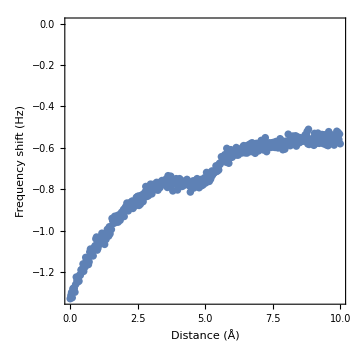
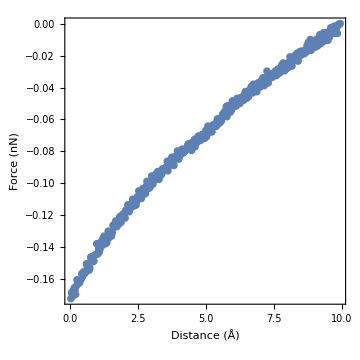

INFLECTION POINT TEST

===================================================================================

Force curve is valid for all amplitudes!

===================================================================================

Uncertainties: 95% C.I.

```mathematica
mainroutine;
finalresult;
writefileCSV;
```